```mathematica
DSolve[d''[x]-a d[x]+b==0,d[x],x]
```

{{d[x]→b/a+ⅇ^(√a x) C[1]+ⅇ^(-√a x) C[2]}}

```mathematica
l=1.0*10^-2;
E0=5.0*10^5;
gc=0.5;
β=(E0 ϵ^2)/(gc l);
α=β+1/l^2;
```

```mathematica
y[x_]:=1/(1+1/(β l^2))+1/(1+β l^2)ⅇ^(-√α x);
```

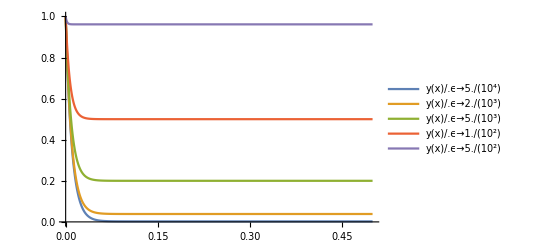

```mathematica
Plot[{y[x]/.ϵ->5.0*10^-4,y[x]/.ϵ->2.0*10^-3,y[x]/.ϵ->5.0*10^-3,y[x]/.ϵ->1.0*10^-2,y[x]/.ϵ->5.0*10^-2},{x,0,0.5},PlotLegends->"Expressions",AspectRatio->0.618,PlotRange->{{0,0.5},{0,1}}]
```